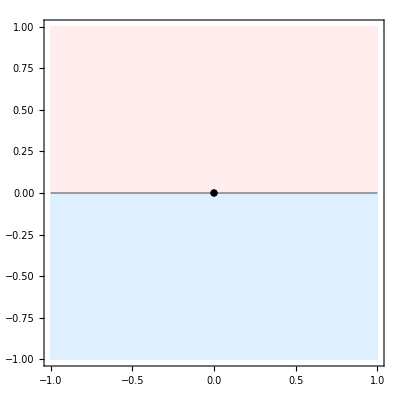

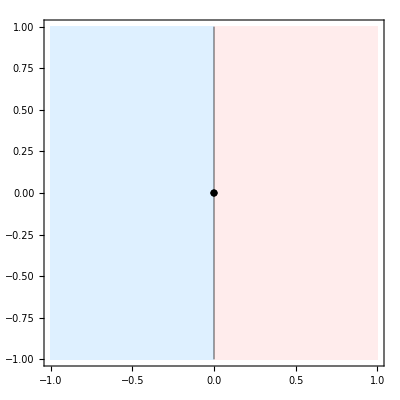

```mathematica
diag=1+I;
proc[f_,a_,b_]:=Module[{cp,lp},
cp=ComplexContourPlot[Im[f],{z,a-b*diag,a+b*diag},
Contours->{0},ContourShading->{LightBlue,LightPink}];
lp=ComplexListPlot[{0},PlotStyle->{Black,size}];
Show[cp,lp]];
u0=proc[z,0,1]
u6=proc[z*I,0,1]
```